## Optimization Exercises Names: Simon Orlovsky and Rebecca DeLand

### 1.

Let f(x,y)=x^3+x y -y^3.

#### Find all critical points for f and use the second derivative test to classify each critical point.

#### Produce a contour plot that shows the important aspects of this function.

```mathematica
f[x_,y_]=x^3+x*y-y^3
```

x^3+x y-y^3

```mathematica
gradf[x_,y_] = D[f[x,y], {{x,y}}] //Simplify
```

{3 x^2+y,x-3 y^2}

```mathematica
Solve[gradf[x,y]=={0,0},{x,y}]
```

{{x→0,y→0}}

```mathematica
d[x_, y_] = Det[({{D[f[x,y], x,x], D[f[x,y], x,y]}, {D[f[x,y], x,y], D[f[x,y], y,y]}})]
```

-1-36 x y

```mathematica
d[0,0]
```

-1

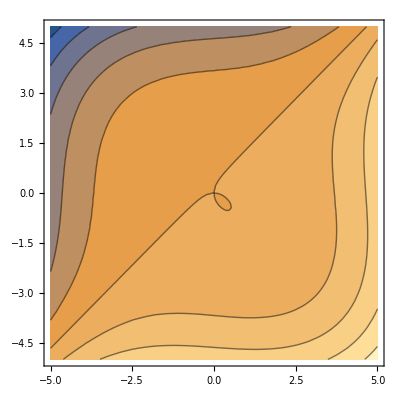

```mathematica
ContourPlot[f[x,y],{x,-5,5},{y,-5,5}]
```

Saddle at f(0,0)=0

### 2.

Let f(x,y)=4+x y-x-y

#### Let D be the closed triangular region with vertices (2,0), (6,0), and (2,4). Find the absolute maximum and minimum values of f on D.

```mathematica
f[x_, y_] = 4+x*y-x-y
```

4-x-y+x y

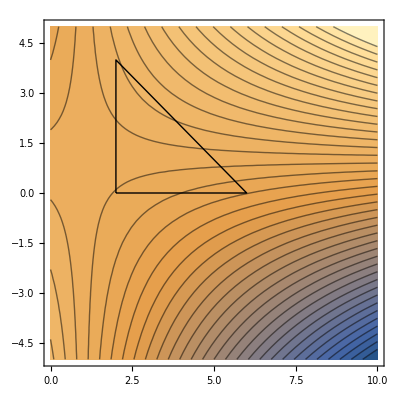

```mathematica
Show[ContourPlot[f[x,y],{x,0,10},{y,-5,5},Contours->40],Graphics[Line[{{2,0},{6,0},{2,4},{2,0}}]]]
```

```mathematica
r[t_] =Simplify[{6,0}+ t*({2,4}-{6,0})]
```

{6-4 t,4 t}

```mathematica
g[t_]=f[6-4t,4t]//Simplify
```

-2+4 (6-4 t) t

```mathematica
g'[t]
```

4 (6-4 t)-16 t

```mathematica
Solve[g'[t]==0]
```

{{t→3/4}}

```mathematica
r[3/4]
```

{3,3}

```mathematica
g[3/4]
```

7

```mathematica
f[6,0]
```

-2

The global minimum is -2 and occurs at the point (6,0)
The global maximum is 7 and occurs at the point (3,3)

### 3.

Let f(x,y)=x y^3

#### Let D={(x,y)|x≥0, y≥0, and x^2+y^2≤4}. Find the absolute maximum and minimum values of f on D.

```mathematica
f[x_, y_] = x*y^3
```

x y^3

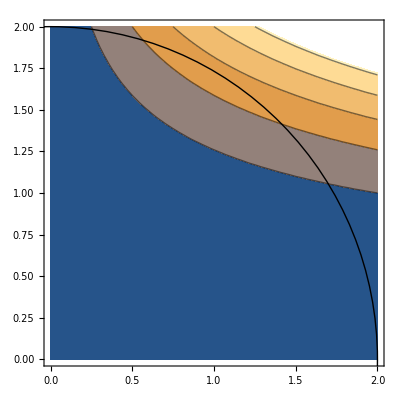

```mathematica
Show[ContourPlot[f[x,y], {x,0, 2},{y, 0, 2}], Graphics[Circle[{0,0},2]]]
```

```mathematica
r[ t_]={2Cos[t],2Sin[t]}
```

{2 Cos[t],2 Sin[t]}

```mathematica
g[t_] = f[2Cos[t], 2Sin[t]] //Simplify
```

16 Cos[t] Sin[t]^3

```mathematica
g'[t]
```

48 Cos[t]^2 Sin[t]^2-16 Sin[t]^4

```mathematica
Clear[g]
```

```mathematica
Solve[g'[t]==0,t]
```

{{t→ConditionalExpression[2 π C[1],C[1]∈Integers]},{t→ConditionalExpression[-(2 π)/3+2 π C[1],C[1]∈Integers]},{t→ConditionalExpression[-π/3+2 π C[1],C[1]∈Integers]},{t→ConditionalExpression[π/3+2 π C[1],C[1]∈Integers]},{t→ConditionalExpression[(2 π)/3+2 π C[1],C[1]∈Integers]},{t→ConditionalExpression[π+2 π C[1],C[1]∈Integers]}}

```mathematica
r[π/3]
```

{1,√3}

```mathematica
g[π/3]
```

3 √3

The global maximum is 3√3 at the point (1, √3)
The global minimum is 0 at the point (2,0) and (0,2)